```mathematica
randomZNestedListu[seznam_]:=Map[RandomChoice,seznam]
```

```mathematica
randomZNestedListu[{{1,2,3,4},{"a","b","c"},{"já","ty"}}]
```

{4,b,já}

```mathematica
f[s_List]:=Map[{#,Count[s,#]}&,Union[s]]
```

```mathematica
f[{1,2,2,3,3,4}]
```

{{1,1},{2,2},{3,2},{4,1}}

```mathematica
"je to funkce 'komprese' z úlohy 7"
```

```mathematica
porovnani[seznam1_,seznam2_]:=MapThread[#1==#2&,{seznam1,seznam2}]
```

```mathematica
porovnani[{1,2,3,4,5},{1,0,3,0,5}]
```

{True,False,True,False,True}

```mathematica
MapThread[List,{{1,2,3},{4,5,6}}]
```

{{1,4},{2,5},{3,6}}

```mathematica
"Transponuje matici"
```

```mathematica
foldFaktorial[n_]:=Fold[Times,1,Range[n]]
```

```mathematica
foldFaktorial[6]
```

720

```mathematica
f[s_List]:=Fold[(10*#1+#2)&,0,s]
```

```mathematica
f[{1,2,0,5,4}]
```

12054

```mathematica
"Ze seznamu cifer dělá číslo"
```

```mathematica
v[n_]:=Nest[Sqrt[1/2+1/2*#]&,Sqrt[1/2],n-1]
```

```mathematica
vietePi[n_]:=2/Product[v[k],{k,1,n}]
```

```mathematica
N[vietePi[20],20]
```

3.1415926535886182366

```mathematica
-Pi
```

-1.175002×10^-12

```mathematica
zajatci[s_List]:=NestList[Rest[RotateLeft[#]]&,s,Length[s]-1]
```

```mathematica
zajatciPoradi[s_List]:=Flatten[Map[#/.{a_,b_,c___}->{b}&,Most[s]]]
```

```mathematica
zajatci[{"a","b","c","d","e"}]
```

{{a,b,c,d,e},{c,d,e,a},{e,a,c},{c,e},{c}}

```mathematica
zajatciPoradi[]
```

{b,d,a,e}

```mathematica
zajatciIndex[s_List]:=Select[s,{#}==Nest[Rest[RotateLeft[#]]&,s,Length[s]-1]&->"Index"]
```

```mathematica
zajatciIndex[{"a","b","c","d","e"}]
```

{3}

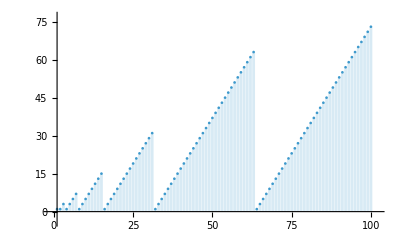

```mathematica
DiscretePlot[zajatciIndex[Range[i]],{i,1,100}]
```

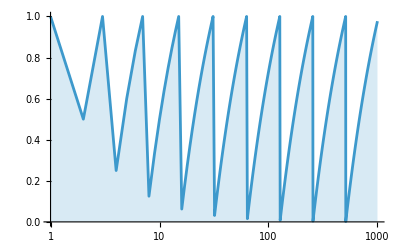

```mathematica
DiscretePlot[{zajatciIndex[Range[i]]/i},{i,1,1000},ScalingFunctions->{"Log",None}]
```

```mathematica
acka[n_]:=IntegerDigits[Range[0,2^n-1],2,n]
zetka[z_,n_]:=Table[z^i,{i,1,n}]
```

```mathematica
mnozinaA[z_,n_]:=Map[Dot[zetka[z,n],Transpose[#]]&,acka[n]]
```

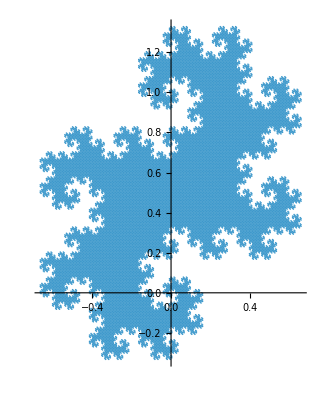

```mathematica
ComplexListPlot[mnozinaA[0.5+0.5I,15]]
```

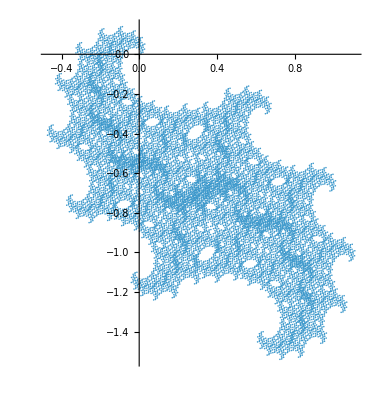

```mathematica
ComplexListPlot[mnozinaA[0.65-0.3I,14]]
```

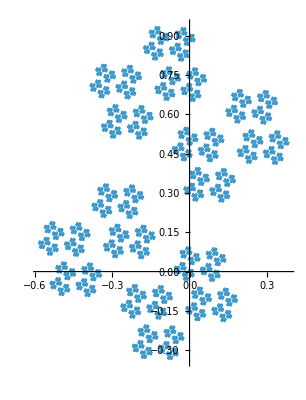

```mathematica
ComplexListPlot[mnozinaA[0.2+0.6I,14]]
```

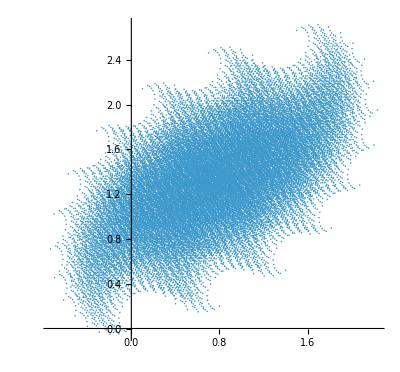

```mathematica
ComplexListPlot[mnozinaA[0.8+0.2I,15]]
```

```mathematica
f[n_,x_]:=Fold[Sqrt[1+#2*#1]&,Sqrt[1+x],Reverse[Range[2,n]]]
```

```mathematica
f[10,0]
```

√(1+2 √(1+3 √(1+4 √(1+5 √(1+6 √(1+7 √(1+8 √(1+9 √11))))))))